```mathematica
Clear["Global`*"];
SeedRandom[0];
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
σ=0.00001;
U[x_]=x^2/(2 σ^2);
dU[x_]=GradientG[U[x],{x}];
ddU[x_]=HessianH[U[x],{x}];
```

```mathematica
QS=hmc[U,dU,ddU,1,5000,10000,True,True,{}];
```

10011.516810.6126460.5274720.5001560.7704542.28727388804.0.00001853880.00135131True{1,3}{1,4}

2002321324.2.20913×10^-100.5331430.4999040.03065461.65716321324.0.00001853880.00135131False{4}{2}

30030.4813480.6103950.4260110.5027161.091951.57329112623.0.00001853880.00263331True{1,4}{1,4}

400476921.41.77071×10^-100.5663880.4988761.719231.9616576923.20.00001853880.00318631False{1,4}{2,3}

50050.6893120.5198920.9736820.04558331.1871.87631112619.0.00001853880.00197845True{1,3}{1,4}

6006112618.8.13615×10^-110.4373840.5036851.043391.87631112619.0.00001853880.00197845False{1,3}{1,4}

7007-0.5505930.08476720.359620.4482852.42691.87631112619.0.00001853880.00197845True{1,3}{1,4}

8008112618.1.04146×10^-100.244540.2894330.8190781.87631112619.0.00001853880.00197845False{1,3}{1,4}

9009-0.1943452.871070.909720.156372.070651.87631112619.0.00001853880.00197845True{1,3}{1,4}

```mathematica
StandardDeviation[QS]
```

{0.0000101646}

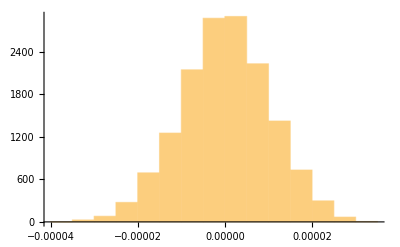

```mathematica
Histogram[QS[[;;,1]]]
```